## BSF History

```mathematica
genomes=ToExpression@StringSplit[Import["~/java/exp/GP_T/run_001_010_O_GENOMES_MATH.txt"],"\n"];
```

Finds the genome id of the BSF. Warning it searches only the last generation!

```mathematica
Flatten[{{a,{b,e}},{c,{d,f}}},1]
```

{a,{b,e},c,{d,f}}

```mathematica
findBSFId[genomes_]:=Sort[Flatten[genomes,1],#1⟦4⟧>#2⟦4⟧&]⟦1,1⟧
```

```mathematica
findBSFId[genomes]
```

998633

```mathematica
traceBackIds[parentId_Integer,genomes_]:=
Module[{p,n,i,l={}},
n=parentId;
For[i=Length[genomes],i≥1,i--,
p=Cases[genomes⟦i⟧,{n,_,_,_}];
If[p=!={},p=Sequence@@p;PrependTo[l,{i}~Join~p];n=p⟦2⟧;,Null];
];
l
]
```

```mathematica
ids=traceBackIds[99999,genomes];
```

```mathematica
ids//MatrixForm;
```

```mathematica
removeDuplicit[ids_]:=
Module[{i,l={},it},
it=ids⟦1⟧;
For[i=2,i<=Length[ids],i++,
(*Print[all[[i,2]]," ",all⟦i-1,2⟧];*)
If[ids⟦i,4⟧=!=ids⟦i-1,4⟧,
AppendTo[l,it];it=ids⟦i⟧, 
Null
]
];
AppendTo[l,it];
l
]
```

```mathematica
removeDuplicit[ids]//MatrixForm;
```

```mathematica
onlyNBiggestChanges[ids_,N_]:=ids⟦Sort[Ordering[Abs[#⟦1⟧-#⟦2⟧]&/@Partition[ids⟦All,5⟧,2,1],-N]]⟧
```

```mathematica
listBSFEvolution[fileName_]:=
Module[{genomes},
genomes=ToExpression@StringSplit[Import[fileName],"\n"];
(*onlyNBiggestChanges[traceBackIds[findBSFId[genomes],genomes],15]*)
removeDuplicit[traceBackIds[findBSFId[genomes],genomes]]
(*traceBackIds[findBSFId[genomes],genomes]*)
]
```

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT_T2/run_001_004_O_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 300010 | -1 | {plus} | 39.0143
3 | 300222 | 300110 | {sin[x1]} | 61.2539
5 | 300474 | 300305 | {plus[1. sin[x1]]} | 61.2539
7 | 300652 | 300536 | {plus[0.779381 sin[x1]]} | 64.5911
9 | 300828 | 300705 | {plus[0.777669 atan[x1]]} | 64.9817
12 | 301151 | 301025 | {plus[0.655925 atan[x1]]} | 65.2379
18 | 301757 | 301607 | {plus[0.566405 times[x1]]} | 65.6833
20 | 301929 | 301805 | {plus[0.566066 times[x1]]} | 65.6837
25 | 302484 | 302309 | {plus[0.559235 times[x1]]} | 65.6905
29 | 302856 | 302769 | {plus[0.562631 times[x1]]} | 65.6871
30 | 302973 | 302856 | {plus[0.562086 times[x1]]} | 65.6876
37 | 303658 | 303579 | {plus[0.5546 times[x1]]} | 65.6951
42 | 304176 | 304049 | {plus[0.545115 times[x1]]} | 65.7046
45 | 304427 | 304327 | {plus[0.540293 times[x1]]} | 65.7094
46 | 304537 | 304427 | {plus[0.539572 times[x1]]} | 65.7102
49 | 304841 | 304726 | {plus[0.538494 times[x1]]} | 65.7112
51 | 305035 | 304951 | {plus[0.538317 times[x1]]} | 65.7114
71 | 307041 | 306929 | {plus[0.537295 times[x1]]} | 65.7114
75 | 307438 | 307344 | {plus[14.7645 times[x1]]} | 0.
77 | 307698 | 307604 | {times[times[x1]]} | 58.963
78 | 307770 | 307698 | {times[atan[x1]]} | 62.0355
82 | 308199 | 308033 | {atan[atan[x1]]} | 63.6448
115 | 311433 | 311323 | {sin[atan[atan[x1]]]} | 64.1545
116 | 311536 | 311433 | {atan[atan[atan[x1]]]} | 64.2485
122 | 312145 | 312027 | {atan[atan[plus[0.591992 x1]]]} | 65.2103
124 | 312357 | 312239 | {atan[times[plus[0.591992 x1]]]} | 65.5735
127 | 312644 | 312540 | {atan[times[plus[0.588575 x1]]]} | 65.574
128 | 312752 | 312644 | {times[times[plus[0.588575 x1]]]} | 65.6287
131 | 313049 | 312926 | {times[times[plus[0.543992 x1]]]} | 65.7057
133 | 313247 | 313138 | {times[times[plus[0.539282 x1]]]} | 65.7105
135 | 313448 | 313338 | {times[times[plus[0.537868 x1]]]} | 65.7119
189 | 318844 | 318727 | {times[times[plus[0.537466 x1]]]} | 65.7119
218 | 321715 | 321608 | {times[times[plus[0.53755 x1]]]} | 65.7122
297 | 329681 | 329510 | {times[sin[plus[-4.4547 x1]],x1]} | 17.7641
298 | 329792 | 329681 | {times[sin[gauss[x1]],x1]} | 61.7864
300 | 329959 | 329891 | {times[gauss[gauss[x1]],x1]} | 63.4523
301 | 330091 | 329959 | {times[gauss[atan[x1]],x1]} | 64.2414
308 | 330747 | 330670 | {times[gauss[atan[x1]],x1,1]} | 64.2414
309 | 330808 | 330747 | {times[gauss[atan[x1]],1,x1]} | 64.2414
310 | 330961 | 330808 | {times[gauss[times[x1,x3]],1,x1]} | 67.7617
314 | 331308 | 331268 | {plus[1.0111 times[gauss[times[x1,x3]],1,x1]]} | 67.7803
315 | 331431 | 331308 | {plus[1.0122 times[gauss[times[x1,x3]],1,x1]]} | 67.7821
316 | 331523 | 331431 | {plus[1.01161 times[gauss[times[x1,x3]],1,x1]]} | 67.7812
324 | 332365 | 332245 | {plus[1.01633 times[gauss[times[x1,x3]],1,x1]]} | 67.7891
325 | 332446 | 332365 | {plus[1.02209 times[gauss[times[x1,x3]],1,x1]]} | 67.7987
327 | 332652 | 332551 | {plus[1.04715 times[gauss[times[x1,x3]],1,x1]]} | 67.8144
331 | 333054 | 332936 | {plus[1.04679 times[gauss[times[x1,x3]],1,x1]]} | 67.8149
335 | 333463 | 333328 | {plus[1.04679 times[gauss[times[x1,x3,x3]],1,x1]]} | 68.5818
356 | 335527 | 335438 | {plus[1.03935 times[gauss[times[x1,x3,x3]],1,x1]]} | 68.5858
390 | 338923 | 338822 | {plus[1.03879 times[gauss[times[x1,x3,x3]],1,x1]]} | 68.5861
405 | 340449 | 340331 | {plus[1.03879 times[gauss[times[x1,x3,x3]],1,x1]]} | 68.5861
432 | 343170 | 343021 | {plus[1.03822 times[gauss[times[x1,x3,x3]],1,x1]]} | 68.5864
481 | 348036 | 347907 | {plus[1.03822 times[gauss[times[x1,x3,x3,x3]],1,x1]]} | 68.7977
498 | 349712 | 349605 | {sin[times[gauss[times[x1,x3,x3,x3],x2],1,x1]]} | 68.0944
499 | 349884 | 349712 | {times[times[gauss[times[x1,x3,x3,x3],x2],1,x1]]} | 69.1746
502 | 350190 | 350069 | {times[times[gauss[times[x1,x3,x3,x3,x1],x2],1,x1]]} | 69.2981
503 | 350275 | 350190 | {times[times[gauss[times[x1,x3,x1,x3,x3],x2],1,x1]]} | 69.2981
509 | 350857 | 350784 | {times[times[gauss[times[sin[x1],x3,x1,x3,x3],x2],1,x1]]} | 69.8277
510 | 350950 | 350857 | {times[times[gauss[times[x3,x1,sin[x1],x3,x3],x2],1,x1]]} | 69.8277
515 | 351454 | 351393 | {times[times[gauss[times[x3,x1,atan[x1],x3,x3],x2],1,x1]]} | 70.1186
517 | 351693 | 351552 | {times[times[gauss[times[x3,x1,gauss[x1],x3,x3],x2],1,x1]]} | 72.3563
530 | 352994 | 352850 | {times[times[gauss[times[x3,x1,gauss[x3],x3,x3],x2],1,x1]]} | 72.085
531 | 353073 | 352994 | {times[times[gauss[times[x3,x1,gauss[x1],x3,gauss[x3]],x2],1,x1]]} | 72.6645
532 | 353191 | 353073 | {times[times[gauss[times[x3,x1,plus[0.368226 x1],x3,gauss[x3]],x2],1,x1]]} | 72.7204
533 | 353259 | 353191 | {times[times[gauss[times[x3,x1,plus[0.368226 x1],x3,gauss[x3],1],x2],1,x1]]} | 72.7204
534 | 353346 | 353259 | {times[times[gauss[times[x3,1,x1,plus[0.368226 x1],x3,gauss[x3]],x2],1,x1]]} | 72.7204
536 | 353546 | 353453 | {times[times[gauss[times[x3,1,x1,plus[0.253801 x1],x3,gauss[x3]],x2],1,x1]]} | 72.7598
539 | 353882 | 353756 | {times[times[gauss[times[x3,1,x1,plus[0.253801 x1],x3,sin[x3]],x2],1,x1]]} | 72.8366
543 | 354302 | 354164 | {times[times[gauss[times[x3,1,x1,plus[0.252797 x1],x3,sin[x3]],x2],1,x1]]} | 72.838
545 | 354496 | 354369 | {plus[1.39093 times[gauss[times[x3,1,x1,plus[0.217013 x1],x3,sin[x3]],x2],1,x1]]} | 74.6971
547 | 354665 | 354592 | {plus[1.39093 times[gauss[times[x3,1,x1,gauss[x1],x3,sin[x3]],x2],1,x1]]} | 75.1295
559 | 355853 | 355734 | {plus[1.37974 times[gauss[times[x3,1,x1,gauss[x1],x3,sin[x3]],x2],1,x1]]} | 75.1506
562 | 356150 | 356048 | {plus[1.35983 times[gauss[times[x3,1,x1,gauss[x1],x3,sin[x3]],x2],1,x1]]} | 75.1882
563 | 356247 | 356150 | {plus[1.35983 times[gauss[times[x3,1,x1,gauss[x1],x3,times[x3]],x2],1,x1]]} | 75.4425
566 | 356571 | 356460 | {plus[1.35983 times[gauss[times[x3,1,x1,gauss[x1],x3,times[x3],1],x2],1,x1]]} | 75.4425
567 | 356656 | 356571 | {plus[1.35983 times[gauss[times[1,x3,1,x1,gauss[x1],x3,times[x3]],x2],1,x1]]} | 75.4425
568 | 356781 | 356656 | {plus[1.35041 times[gauss[times[1,x3,1,x1,gauss[x1],x3,times[x3]],x2],1,x1]]} | 75.4502
571 | 357077 | 356952 | {plus[1.35041 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,times[x3]],x2],1,x1]]} | 75.4635
573 | 357260 | 357149 | {plus[1.40183 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,times[x3]],x2],1,x1]]} | 75.5095
576 | 357517 | 357413 | {plus[1.40081 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,plus[2.16191 x3]],x2],1,x1]]} | 76.0525
582 | 358120 | 358005 | {plus[1.44608 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,plus[2.1572 x3]],x2],1,x1]]} | 76.1682
589 | 358810 | 358781 | {plus[1.44608 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,plus[2.16592 x3]],x2],1,x1]]} | 76.1688
590 | 358913 | 358810 | {plus[1.44905 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,plus[2.16592 x3]],x2],1,x1]]} | 76.1721
593 | 359212 | 359111 | {plus[1.44905 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,plus[2.16592 x3],x3],x2],1,x1]]} | 77.5339
594 | 359305 | 359212 | {plus[1.44905 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[2.16592 x3]],x2],1,x1]]} | 77.5339
597 | 359627 | 359513 | {plus[1.43791 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[2.16592 x3],x3],x2],1,x1]]} | 77.9053
601 | 360022 | 359906 | {plus[1.43791 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[4.08762 x3],x3],x2],1,x1]]} | 78.3981
606 | 360595 | 360405 | {plus[1.44613 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.32557 x3],x3],x2],1,x1]]} | 78.5394
608 | 360802 | 360685 | {plus[1.47718 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.32557 x3],x3],x2],1,x1]]} | 78.5873
609 | 360885 | 360802 | {plus[1.48787 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.32877 x3],x3],x2],1,x1]]} | 78.6027
610 | 360993 | 360885 | {plus[1.48039 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.32528 x3],x3],x2],1,x1]]} | 78.5912
612 | 361169 | 361083 | {plus[1.49844 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.49023 x3],x3],x2],1,x1]]} | 78.6226
613 | 361270 | 361169 | {plus[1.52987 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.48704 x3],x3],x2],1,x1]]} | 78.6339
617 | 361687 | 361581 | {plus[1.52431 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.48704 x3],x3],x2],1,x1]]} | 78.6352
618 | 361785 | 361687 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.48922 x3],x3],x2],1,x1]]} | 78.6386
622 | 362185 | 362084 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.47545 x3],x3],x2],1,x1]]} | 78.6394
623 | 362302 | 362185 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.46591 x3],x3],x2],1,x1]]} | 78.64
627 | 362609 | 362563 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.41962 x3],x3],x2],1,x1]]} | 78.6433
633 | 363281 | 363110 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.4112 x3],x3],x2],1,x1]]} | 78.644
637 | 363661 | 363550 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.4112 x3,1. x2],x3],x2],1,x1]]} | 78.9357
638 | 363751 | 363661 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-4.4112 x3,1.01039 x2],x3],x2],1,x1]]} | 78.9383
640 | 363974 | 363871 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[4.91769 x3,1.50897 x2],x3],x2],1,x1]]} | 78.9508
646 | 364563 | 364451 | {plus[1.50932 times[gauss[times[1,x3,1,x1,gauss[x1,1],x3,x3,plus[-3.52444 x3,1.50897 x2],x3],x2],1,x1]]} | 79.2667
652 | 365187 | 365006 | {plus[1.50932 times[gauss[times[1,x3,1,x1,times[x1,1],x3,x3,plus[-0.396099 x3,1.50897 x2],x3],x2],1,x1]]} | 81.7184
656 | 365576 | 365451 | {plus[1.50932 times[gauss[times[1,x3,1,x1,times[x1,1],x3,x3,plus[0.351311 x3,1.50897 x2],x3],x2],1,x1]]} | 81.8226
658 | 365766 | 365654 | {plus[1.50932 times[gauss[times[1,x3,1,x1,times[x1,1],x3,x3,plus[0.372291 x3,1.66191 x2],x3],x2],1,x1]]} | 82.033
660 | 365960 | 365867 | {plus[1.50932 times[gauss[times[1,x3,1,x1,times[x1,1],x3,x3,plus[0.372291 x3,1.66191 x2],x3,1],x2],1,x1]]} | 82.033
661 | 366055 | 365960 | {plus[1.50932 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.372291 x3,1.66191 x2],x3],x2],1,x1]]} | 82.033
662 | 366174 | 366055 | {plus[1.50932 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.376868 x3,1.901 x2],x3],x2],1,x1]]} | 82.1426
667 | 366662 | 366549 | {plus[1.50932 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,1.901 x2],x3],x2],1,x1]]} | 82.5038
674 | 367351 | 367234 | {plus[1.52353 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,1.901 x2],x3],x2],1,x1]]} | 82.5602
677 | 367647 | 367530 | {plus[1.52353 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.26611 x2],x3],x2],1,x1]]} | 83.6729
684 | 368354 | 368227 | {plus[1.53622 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.26611 x2],x3],x2],1,x1]]} | 83.7326
690 | 368949 | 368834 | {plus[1.53622 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.3106 x2],x3],x2],1,x1]]} | 83.8669
692 | 369152 | 369027 | {plus[1.53622 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.3112 x2],x3],x2],1,x1]]} | 83.8687
697 | 369650 | 369530 | {plus[1.53622 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.31866 x2],x3],x2],1,x1]]} | 83.8766
701 | 370040 | 369934 | {plus[1.54867 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.31866 x2],x3],x2],1,x1]]} | 83.9112
703 | 370248 | 370128 | {plus[1.54867 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.33518 x2],x3],x2],1,x1]]} | 83.9274
709 | 370845 | 370726 | {plus[1.54867 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.717489 x3,2.65316 x2],x3],x2],1,x1]]} | 84.0544
712 | 371137 | 371030 | {plus[1.54867 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.723382 x3,2.65316 x2],x3],x2],1,x1]]} | 84.0843
717 | 371637 | 371522 | {plus[1.54867 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.764682 x3,2.65316 x2],x3],x2],1,x1]]} | 84.1633
721 | 372056 | 371931 | {plus[1.60971 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.765655 x3,2.64972 x2],x3],x2],1,x1]]} | 84.3471
722 | 372115 | 372056 | {plus[1.60971 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.765655 x3,2.64172 x2],x3],x2],1,x1]]} | 84.3419
725 | 372425 | 372306 | {plus[1.60971 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[-0.765655 x3,2.92333 x2],x3],x2],1,x1]]} | 84.4669
730 | 372927 | 372805 | {plus[1.60971 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.849082 x3,2.92886 x2],x3],x2],1,x1]]} | 84.4671
742 | 374123 | 374007 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.849082 x3,2.93198 x2],x3],x2],1,x1]]} | 84.4678
746 | 374512 | 374412 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.839888 x3,2.93198 x2],x3],x2],1,x1]]} | 84.4697
748 | 374709 | 374605 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.797969 x3,2.93198 x2],x3],x2],1,x1]]} | 84.4709
751 | 375013 | 374907 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.797969 x3,2.96614 x2],x3],x2],1,x1]]} | 84.4851
760 | 375924 | 375805 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.787726 x3,2.96614 x2],x3],x2],1,x1]]} | 84.4855
768 | 376728 | 376606 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.787726 x3,2.97269 x2],x3],x2],1,x1]]} | 84.487
771 | 377012 | 376914 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.787726 x3,2.97264 x2],x3],x2],1,x1]]} | 84.4871
776 | 377533 | 377408 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.794695 x3,2.97264 x2],x3],x2],1,x1]]} | 84.4879
784 | 378320 | 378209 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.794695 x3,2.98816 x2],x3],x2],1,x1]]} | 84.4901
788 | 378716 | 378606 | {plus[1.60537 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.801975 x3,2.98816 x2],x3],x2],1,x1]]} | 84.4938
794 | 379323 | 379231 | {plus[1.61187 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.801975 x3,3.00257 x2],x3],x2],1,x1]]} | 84.4985
815 | 381419 | 381305 | {plus[1.60971 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.801975 x3,3.00257 x2],x3],x2],1,x1]]} | 84.4992
819 | 381816 | 381727 | {plus[1.60867 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.807015 x3,3.00257 x2],x3],x2],1,x1]]} | 84.4993
820 | 381922 | 381816 | {plus[1.60867 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.81137 x3,3.00257 x2],x3],x2],1,x1]]} | 84.4992
821 | 382036 | 381922 | {plus[1.60758 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.81137 x3,3.00257 x2],x3],x2],1,x1]]} | 84.4995
825 | 382426 | 382306 | {plus[1.60839 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.81137 x3,3.00783 x2],x3],x2],1,x1]]} | 84.5015
833 | 383222 | 383108 | {plus[1.60839 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.81137 x3,3.01184 x2],x3],x2],1,x1]]} | 84.5023
863 | 386213 | 386107 | {plus[1.61999 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.81137 x3,3.02217 x2],x3],x2],1,x1]]} | 84.5043
866 | 386516 | 386405 | {plus[1.61999 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.814904 x3,3.02217 x2],x3],x2],1,x1]]} | 84.5042
867 | 386614 | 386516 | {plus[1.61999 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.814904 x3,3.02945 x2],x3],x2],1,x1]]} | 84.5069
870 | 386923 | 386805 | {plus[1.61999 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.813386 x3,3.02945 x2],x3],x2],1,x1]]} | 84.5073
880 | 387915 | 387806 | {plus[1.61999 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.812842 x3,3.02945 x2],x3],x2],1,x1]]} | 84.5074
904 | 390309 | 390206 | {plus[1.61932 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.812842 x3,3.02945 x2],x3],x2],1,x1]]} | 84.5075
929 | 392814 | 392709 | {plus[1.61932 times[gauss[times[1,1,x3,1,x1,times[x1,1],x3,x3,plus[0.812842 x3,3.02945 x2],x3],x2],1,x1]]} | 84.5075)

```mathematica
(evo2=listBSFEvolution["~/java/exp/GP_T/run_001_003_O_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 200098 | -1 | {x1} | 58.963
2 | 200162 | 200098 | {times[x0,gauss[x0]]} | 25.5012
3 | 200208 | 200162 | {times[x1,gauss[x0]]} | 61.8045
5 | 200437 | 200208 | {times[x1,gauss[atan[x3]]]} | 69.0813
7 | 200618 | 200437 | {times[x1,gauss[x1]]} | 61.5408
10 | 200937 | 200618 | {times[x1,gauss[times[x3,-1.]]]} | 70.0646
11 | 201092 | 200937 | {times[x1,gauss[times[x3,x2]]]} | 71.1302
12 | 201196 | 201092 | {times[x1,gauss[times[-1.,x2]]]} | 72.7854
19 | 201891 | 201196 | {times[x1,gauss[times[x2,x2]]]} | 73.7491
25 | 202469 | 202311 | {times[x1,gauss[times[x2,plus[0.088203,-1.]]]]} | 72.8331
28 | 202729 | 202469 | {times[x1,gauss[times[x2,plus[0.0886965,-1.]]]]} | 72.8303
31 | 203082 | 202729 | {times[x1,gauss[times[x2,plus[0.088246,-1.]]]]} | 72.8329
33 | 203228 | 203082 | {times[x1,gauss[times[x2,plus[0.0763921,-1.]]]]} | 72.8643
40 | 203929 | 203228 | {times[x1,gauss[times[x2,plus[x3,x3]]]]} | 75.3021
83 | 208225 | 205128 | {times[x1,gauss[times[x2,plus[sin[x3],x3]]]]} | 75.8776
85 | 208476 | 208225 | {times[x1,gauss[times[times[x2,sin[4.86918]],plus[sin[x3],x3]]]]} | 76.038
86 | 208584 | 208476 | {times[x1,gauss[times[times[x2,-1.],plus[sin[x3],x3]]]]} | 75.8776
87 | 208685 | 208584 | {times[x1,gauss[times[times[x2,0.90841],plus[sin[x3],x3]]]]} | 76.6067
91 | 209102 | 208685 | {times[x1,gauss[times[times[x2,0.923921],plus[sin[x3],x3]]]]} | 76.5214
98 | 209793 | 209102 | {times[x1,gauss[times[times[x2,0.887931],plus[sin[x3],x3]]]]} | 76.6847
117 | 211616 | 209793 | {times[x1,gauss[times[times[x2,0.887931],plus[sin[x3],atan[x3]]]]]} | 76.9509
119 | 211847 | 211616 | {times[x1,gauss[times[times[x2,0.901474],plus[sin[x3],atan[x3]]]]]} | 76.9689
135 | 213477 | 212241 | {times[x1,gauss[times[times[x2,0.902736],plus[sin[x3],atan[x3]]]]]} | 76.9708
136 | 213520 | 213477 | {times[x1,gauss[times[times[x2,0.903798],plus[sin[x3],atan[x3]]]]]} | 76.9724
159 | 215852 | 215537 | {times[x1,gauss[times[times[x2,0.903798],plus[atan[x3],atan[x3]]]]]} | 77.0018
160 | 215952 | 215852 | {times[x1,gauss[times[times[x2,0.919803],plus[atan[x3],atan[x3]]]]]} | 77.038
170 | 216907 | 216761 | {times[x1,gauss[times[times[x2,0.91821],plus[atan[x3],atan[x3]]]]]} | 77.0368
173 | 217275 | 216907 | {times[x1,gauss[times[times[x2,0.915685],plus[atan[x3],atan[x3]]]]]} | 77.034
187 | 218685 | 218407 | {times[x1,gauss[times[times[x2,0.916981],plus[atan[x3],atan[x3]]]]]} | 77.0354
199 | 219877 | 218685 | {times[x1,gauss[times[times[x2,0.919596],plus[atan[x3],atan[x3]]]]]} | 77.0384
341 | 234043 | 225282 | {times[x1,gauss[times[times[x2,0.919698],plus[atan[x3],atan[x3]]]]]} | 77.0385
833 | 283205 | 238983 | {times[times[1.31884,x1],gauss[times[times[x2,0.919698],plus[atan[x3],atan[x3]]]]]} | 77.3475
840 | 283945 | 283205 | {times[times[1.31867,x1],gauss[times[times[x2,0.919698],plus[atan[x3],atan[x3]]]]]} | 77.3492
843 | 284260 | 283945 | {times[times[1.31867,x1],gauss[times[times[x2,0.925856],plus[atan[x3],atan[x3]]]]]} | 77.4892
848 | 284760 | 284560 | {times[times[1.31867,x1],gauss[times[times[x2,1.10323],plus[atan[x3],atan[x3]]]]]} | 79.4324
850 | 284996 | 284760 | {times[times[1.40053,x1],gauss[times[times[x2,1.10323],plus[atan[x3],atan[x3]]]]]} | 79.9069
857 | 285692 | 285365 | {times[times[1.40053,x1],gauss[times[times[x2,1.11416],plus[atan[x3],atan[x3]]]]]} | 80.0406
864 | 286346 | 286091 | {times[times[1.4006,x1],gauss[times[times[x2,1.11416],plus[atan[x3],atan[x3]]]]]} | 80.0408
866 | 286601 | 286346 | {times[times[1.4006,x1],gauss[times[times[x2,1.11416],plus[atan[x3],x3]]]]} | 80.1215
869 | 286864 | 286634 | {times[times[1.4006,x1],gauss[times[times[x2,1.13401],plus[atan[x3],x3]]]]} | 80.0506
874 | 287322 | 286864 | {times[times[1.47337,x1],gauss[times[times[x2,1.13401],plus[atan[x3],x3]]]]} | 80.6333
884 | 288371 | 287322 | {times[times[1.47227,x1],gauss[times[times[x2,1.13401],plus[atan[x3],x3]]]]} | 80.6312
885 | 288445 | 288371 | {times[times[1.48075,x1],gauss[times[times[x2,1.13401],plus[atan[x3],x3]]]]} | 80.601
893 | 289302 | 288628 | {times[times[1.48075,x1],gauss[times[times[x2,1.13401],plus[sin[x3],x3]]]]} | 80.6644
900 | 289978 | 289302 | {times[times[1.48075,x1],gauss[times[times[x2,1.13697],plus[sin[x3],x3]]]]} | 80.6453
909 | 290844 | 289978 | {times[times[1.48407,x1],gauss[times[times[x2,1.13697],plus[sin[x3],x3]]]]} | 80.6553
912 | 291179 | 290844 | {times[times[1.48407,x1],gauss[times[times[x2,1.12911],plus[sin[x3],x3]]]]} | 80.6907
924 | 292368 | 291179 | {times[times[1.48407,x1],gauss[times[times[x2,1.13078],plus[sin[x3],x3]]]]} | 80.6948
957 | 295651 | 292368 | {times[times[1.48439,x1],gauss[times[times[x2,1.13078],plus[sin[x3],x3]]]]} | 80.6954
994 | 299398 | 298405 | {times[times[1.4849,x1],gauss[times[times[x2,1.13078],plus[sin[x3],x3]]]]} | 80.696)

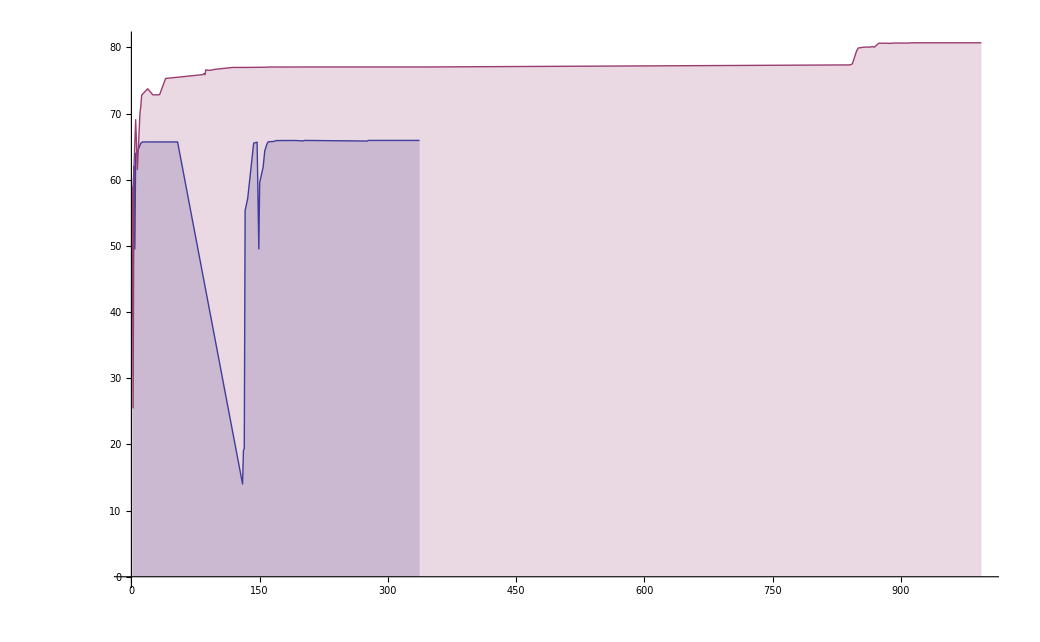

```mathematica
ListLinePlot[{evo1⟦All,{1,5}⟧,evo2⟦All,{1,5}⟧},Filling->Axis]
```